Here is the file to seek possible solutions of differential equation.

```mathematica
(*Quit*)
```

## 尝试直接解z方向微分方程

```mathematica
(* Below is a simple test *)
DSolve[y'''[x] -4*y''[x]-25*y'[x]+28*y[x]==0, y[x], x]
```

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^x C[2]+ⅇ^(7 x) C[3]}}

```mathematica
DSolve[{(z[t])^(3/2)*z''[t]+ξ*z'[t]==0,z[0]==za},z[t],t]
```

{{z[t]→InverseFunction[(8 ξ^2 Log[2 ξ+C[1] √#1])/C[1]^3-(4 ξ √#1)/C[1]^2+#1/C[1]&][t+(-4 √za ξ C[1]+za C[1]^2+8 ξ^2 Log[2 ξ+√za C[1]])/C[1]^3]}}

```mathematica
(* Could not solve the eq directly w/ Cos[α]==1 *)
DSolve[{z''[t]+ξ*z'[t]/(z[t])^(3/2)+1==0},z[t],t]
```

DSolve[{1+(ξ z'[t])/z[t]^(3/2)+z''[t]==0},z[t],t]

```mathematica
(* Same result as that above *)
DSolve[(z[t])^(3/2)*z''[t]+ξ*z'[t]+(z[t])^(3/2)==0, z[t], t]
```

DSolve[z[t]^(3/2)+ξ z'[t]+z[t]^(3/2) z''[t]==0,z[t],t]

```mathematica
Solve[3x-2y==5&&x+y==0,{x,y}]
```

{{x→1,y→-1}}

## 一阶修正Laplace变换

### 方法一，直接暴力求解

```mathematica
(*联立方程组解出含κ一阶修正时x/θ两方向速度的Laplace变换,wtdx=widetilde{vx},wtdt=widetilde{vt}*)
FullSimplify[Solve[s*wtdx-Subscript[v, x][0]==-Subscript[γ, 0,xx]*wtdx-Subscript[γ, 0,xθ]*wtdt+A&&s*wtdt-Subscript[v, θ][0]==-Subscript[γ, 0,θx]*wtdx-Subscript[γ, 0,θθ]*wtdt+B,{wtdx,wtdt}]]
```

{{wtdx→(-(s+γ_(0,θθ)) (A+v_x[0])+γ_(0,xθ) (B+v_θ[0]))/(γ_(0,xθ) γ_(0,θx)-s (s+γ_(0,θθ))-γ_(0,xx) (s+γ_(0,θθ))),wtdt→(-γ_(0,θx) (A+v_x[0])+s (B+v_θ[0])+γ_(0,xx) (B+v_θ[0]))/(-γ_(0,xθ) γ_(0,θx)+s (s+γ_(0,θθ))+γ_(0,xx) (s+γ_(0,θθ)))}}

说明，A、B分别为：
A = (M^-1)_xx LaplaceTransform[δF_x[t],t,s] + (M^-1)_xθ LaplaceTransform[δF_θ[t],t,s]
B= (M^-1)_θx LaplaceTransform[δF_x[t],t,s] + (M^-1)_θθ LaplaceTransform[δF_θ[t],t,s]

```mathematica
(*Subscript[求v, x] 的Laplace变换，不含噪音*)
FullSimplify[InverseLaplaceTransform[(-(s+Subscript[γ, 0,θθ]) (0*A+Subscript[v, x][0])+Subscript[γ, 0,xθ] (0*B+Subscript[v, θ][0]))/(Subscript[γ, 0,xθ] Subscript[γ, 0,θx]-s (s+Subscript[γ, 0,θθ])-Subscript[γ, 0,xx] (s+Subscript[γ, 0,θθ])),s,t]]
```

1/(2 √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2))ⅇ^(-1/2 t (γ_(0,xx)+√(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)+γ_(0,θθ))) (√(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2) v_x[0]+ⅇ^(t √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)) √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2) v_x[0]+(γ_(0,xx)-γ_(0,θθ)) v_x[0]+2 γ_(0,xθ) v_θ[0]+ⅇ^(t √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)) ((-γ_(0,xx)+γ_(0,θθ)) v_x[0]-2 γ_(0,xθ) v_θ[0]))

```mathematica
(*Subscript[求v, x] 的Laplace变换，仅噪音解不出*)
FullSimplify[InverseLaplaceTransform[(-(s+Subscript[γ, 0,θθ]) (Subscript[(M^-1), xx] LaplaceTransform[Subscript[δF, x][t],t,s] + Subscript[(M^-1), xθ] LaplaceTransform[Subscript[δF, θ][t],t,s])+Subscript[γ, 0,xθ] ( Subscript[(M^-1), θx] LaplaceTransform[Subscript[δF, x][t],t,s] + Subscript[(M^-1), θθ] LaplaceTransform[Subscript[δF, θ][t],t,s]+Subscript[v, θ][0]))/(Subscript[γ, 0,xθ] Subscript[γ, 0,θx]-s (s+Subscript[γ, 0,θθ])-Subscript[γ, 0,xx] (s+Subscript[γ, 0,θθ])),s,t]]
```

InverseLaplaceTransform[(-(LaplaceTransform[δF_x[t],t,s] (1/M)_xx+LaplaceTransform[δF_θ[t],t,s] (1/M)_xθ) (s+γ_(0,θθ))+γ_(0,xθ) (LaplaceTransform[δF_x[t],t,s] (1/M)_θx+LaplaceTransform[δF_θ[t],t,s] (1/M)_θθ+v_θ[0]))/(γ_(0,xθ) γ_(0,θx)-s (s+γ_(0,θθ))-γ_(0,xx) (s+γ_(0,θθ))),s,t]

```mathematica
(*Subscript[求v, x] 的Laplace变换，除去噪音本身变换*)
FullSimplify[InverseLaplaceTransform[(-(s+Subscript[γ, 0,θθ]) (Subscript[(M^-1), xx] + Subscript[(M^-1), xθ] LaplaceTransform[Subscript[δF, θ][t],t,s]*0)+Subscript[γ, 0,xθ] ( Subscript[(M^-1), θx]  + Subscript[(M^-1), θθ] LaplaceTransform[Subscript[δF, θ][t],t,s]*0+Subscript[v, θ][0]))/(Subscript[γ, 0,xθ] Subscript[γ, 0,θx]-s (s+Subscript[γ, 0,θθ])-Subscript[γ, 0,xx] (s+Subscript[γ, 0,θθ])),s,t]]
```

1/(2 √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2))ⅇ^(-1/2 t (γ_(0,xx)+√(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)+γ_(0,θθ))) ((1/M)_xx √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)+ⅇ^(t √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)) (1/M)_xx √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)+(1/M)_xx (γ_(0,xx)-γ_(0,θθ))+2 γ_(0,xθ) v_θ[0]+ⅇ^(t √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)) ((1/M)_xx (-γ_(0,xx)+γ_(0,θθ))-2 γ_(0,xθ) v_θ[0]))

```mathematica
(*Subscript[求v, θ] 的Laplace变换，不含噪音*)
FullSimplify[InverseLaplaceTransform[(-Subscript[γ, 0,θx] (A*0+Subscript[v, x][0])+s (B*0+Subscript[v, θ][0])+Subscript[γ, 0,xx] (B*0+Subscript[v, θ][0]))/(-Subscript[γ, 0,xθ] Subscript[γ, 0,θx]+s (s+Subscript[γ, 0,θθ])+Subscript[γ, 0,xx] (s+Subscript[γ, 0,θθ])),s,t]]
```

1/(2 √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2))ⅇ^(-1/2 t (γ_(0,xx)+√(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)+γ_(0,θθ))) (-2 (-1+ⅇ^(t √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2))) γ_(0,θx) v_x[0]-γ_(0,xx) v_θ[0]+(√(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)+ⅇ^(t √(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)) (γ_(0,xx)+√(4 γ_(0,xθ) γ_(0,θx)+(γ_(0,xx)-γ_(0,θθ))^2)-γ_(0,θθ))+γ_(0,θθ)) v_θ[0])

γ_s= √(4 γ_(0xθ)γ_(0θx)+(γ_(0θθ)-γ_(0xx))^2)

```mathematica
(*Subscript[引入新系数γ, s]*)
FullSimplify[√(4((κ*ξ^2 ϵ^2)/(9 Δ^3))^2+((4ξϵ)/(3 √Δ)+(2κ*ξ^2 ϵ^2)/(9 Δ^3)-((2ξϵ)/(3 √Δ)+(κ*ξ^2 ϵ^2)/(18 Δ^3)))^2)]
```

1/18 √((16 ϵ^4 κ^2 ξ^4+9 (ϵ^2 κ ξ^2+4 Δ^(5/2) ξϵ)^2)/Δ^6)

```mathematica
(*新系数展开*)
Series[√(4((κ*ξ^2*ϵ^2)/(9 Δ^3))^2+((4*ξ*ϵ)/(3 √Δ)+(2κ*ξ^2*ϵ^2)/(9 Δ^3)-((2*ξ*ϵ)/(3 √Δ)+(κ*ξ^2*ϵ^2)/(18 Δ^3)))^2),{κ,0,3}]
```

2/3 √((ϵ^2 ξ^2)/Δ)+(ϵ ξ √((ϵ^2 ξ^2)/Δ) κ)/(6 Δ^(5/2))+(ϵ^2 ξ^2 √((ϵ^2 ξ^2)/Δ) κ^2)/(27 Δ^5)-((ϵ^3 ξ^3 √((ϵ^2 ξ^2)/Δ)) κ^3)/(108 Δ^(15/2))+O[κ]^4

### 方法二，微扰修正

v_z1

```mathematica
InverseLaplaceTransform[(-Subscript[γ, 0,zz1])/(s+Subscript[γ, 0,zz0])^2,s,t]
```

-ⅇ^(-t γ_(0,zz0)) t γ_(0,zz1)

```mathematica
InverseLaplaceTransform[1/(s+Subscript[γ, 0,zz0]),s,t]
```

ⅇ^(-t γ_(0,zz0))

```mathematica
LaplaceTransform[Integrate[f[τ]*g[t-τ],{τ,0,t}],t,s]
```

LaplaceTransform[f[t],t,s] LaplaceTransform[g[t],t,s]

```mathematica
Apart[Integrate[Exp[-2*Subscript[γ, 0,zz0]*(t-τ)]/Subscript[m, z]*(Subscript[(M^-1), zz1]-Subscript[γ, 0,zz1]*(t-τ)*Subscript[(M^-1), zz0])*2 Subscript[k, B]*T*Subscript[m, z]*Subscript[γ, 0,zz0],{τ,0,t}]]
```

(T k_B (2 (1/M)_zz1 γ_(0,zz0)-(1/M)_zz0 γ_(0,zz1)))/(2 γ_(0,zz0))-(ⅇ^(-2 t γ_(0,zz0)) T k_B (2 (1/M)_zz1 γ_(0,zz0)-(1/M)_zz0 γ_(0,zz1)-2 t (1/M)_zz0 γ_(0,zz0) γ_(0,zz1)))/(2 γ_(0,zz0))

```mathematica
Limit[(Subscript[k, B]*T)/Subscript[m, z]*(1-Exp[-2*Subscript[γ, 0,zz0]*t])+Subscript[k, B]*T*(Subscript[(M^-1), zz1]*(1-Exp[-2*Subscript[γ, 0,zz0]*t])+(Subscript[γ, 0,zz1]*Subscript[(M^-1), zz0])/(2 Subscript[γ, 0,zz0])*Exp[-2*Subscript[γ, 0,zz0]*t]*(1-Exp[2*Subscript[γ, 0,zz0]*t]+2 Subscript[γ, 0,zz0]*t)),t->Infinity]
```

ConditionalExpression[T k_B (1/m_z+(1/M)_zz1-((1/M)_zz0 γ_(0,zz1))/(2 γ_(0,zz0))),(T|k_B|1/m_z|(1/M)_zz1|(1/M)_zz0|γ_(0,zz1))∈ℝ&&γ_(0,zz0)>0]

```mathematica
Integrate[Exp[-2*Subscript[γ, 0,zz0]*(t-τ)],{τ,0,t}]
```

-(-1+ⅇ^(-2 t γ_(0,zz0)))/(2 γ_(0,zz0))

v_x1

```mathematica
InverseLaplaceTransform[1/(s+Subscript[γ, 0,xx0])((-Subscript[γ, 0,xx1]*Subscript[v, x][0])/(s+Subscript[γ, 0,xx0])+(-Subscript[γ, 0,xθ1]*Subscript[v, θ][0])/(s+Subscript[γ, 0,θθ0])),s,t]
```

-ⅇ^(-t γ_(0,xx0)) t γ_(0,xx1) v_x[0]+(ⅇ^(-t γ_(0,xx0)) γ_(0,xθ1) v_θ[0])/(γ_(0,xx0)-γ_(0,θθ0))-(ⅇ^(-t γ_(0,θθ0)) γ_(0,xθ1) v_θ[0])/(γ_(0,xx0)-γ_(0,θθ0))

```mathematica
(*MMA could not furnish the correct result for convolution LT.*)
FullSimplify[LaplaceTransform[Integrate[(Subscript[F, x][t])/m*Exp[-γ*(t-τ)],{τ,0,t}],t,s]]
```

(LaplaceTransform[F_x[t],t,s]-LaplaceTransform[F_x[t],t,s+γ])/(m γ)

```mathematica
(*term 1*)
InverseLaplaceTransform[1/(s+Subscript[γ, 0,xx0])*(-Subscript[γ, 0,xx1]*Subscript[(M^-1), xx0])/(s+Subscript[γ, 0,xx0]),s,t]
```

-ⅇ^(-t γ_(0,xx0)) t (1/M)_xx0 γ_(0,xx1)

```mathematica
(*term 2*)
InverseLaplaceTransform[1/(s+Subscript[γ, 0,xx0])*(-Subscript[γ, 0,xθ1]*Subscript[(M^-1), θθ0])/(s+Subscript[γ, 0,θθ0]),s,t]
```

-(1/M)_θθ0 γ_(0,xθ1) (ⅇ^(-t γ_(0,θθ0))/(γ_(0,xx0)-γ_(0,θθ0))+ⅇ^(-t γ_(0,xx0))/(-γ_(0,xx0)+γ_(0,θθ0)))

```mathematica
(*term 3,4*)
InverseLaplaceTransform[Subscript[(M^-1), xx1]/(s+Subscript[γ, 0,xx0]),s,t]
InverseLaplaceTransform[Subscript[(M^-1), xθ1]/(s+Subscript[γ, 0,xx0]),s,t]
```

ⅇ^(-t γ_(0,xx0)) (1/M)_xx1

ⅇ^(-t γ_(0,xx0)) (1/M)_xθ1

v_θ1

```mathematica
InverseLaplaceTransform[1/(s+Subscript[γ, 0,θθ0])((-Subscript[γ, 0,θx1]*Subscript[v, x][0])/(s+Subscript[γ, 0,xx0])+(-Subscript[γ, 0,θθ1]*Subscript[v, θ][0])/(s+Subscript[γ, 0,θθ0])),s,t]
```

(ⅇ^(-t γ_(0,xx0)) γ_(0,θx1) v_x[0])/(γ_(0,xx0)-γ_(0,θθ0))-(ⅇ^(-t γ_(0,θθ0)) γ_(0,θx1) v_x[0])/(γ_(0,xx0)-γ_(0,θθ0))-ⅇ^(-t γ_(0,θθ0)) t γ_(0,θθ1) v_θ[0]

```mathematica
(*term 1*)
InverseLaplaceTransform[1/(s+Subscript[γ, 0,θθ0])*(-Subscript[γ, 0,θx1]*Subscript[(M^-1), xx0])/(s+Subscript[γ, 0,xx0]),s,t]
```

-(1/M)_xx0 γ_(0,θx1) (ⅇ^(-t γ_(0,θθ0))/(γ_(0,xx0)-γ_(0,θθ0))+ⅇ^(-t γ_(0,xx0))/(-γ_(0,xx0)+γ_(0,θθ0)))

```mathematica
(*term 2*)
InverseLaplaceTransform[1/(s+Subscript[γ, 0,θθ0])*(-Subscript[γ, 0,θθ1]*Subscript[(M^-1), θθ0])/(s+Subscript[γ, 0,θθ0]),s,t]
```

-ⅇ^(-t γ_(0,θθ0)) t (1/M)_θθ0 γ_(0,θθ1)

```mathematica
(*term 3,4*)
InverseLaplaceTransform[Subscript[(M^-1), θx1]/(s+Subscript[γ, 0,θθ0]),s,t]
InverseLaplaceTransform[Subscript[(M^-1), θθ1]/(s+Subscript[γ, 0,θθ0]),s,t]
```

ⅇ^(-t γ_(0,θθ0)) (1/M)_θx1

ⅇ^(-t γ_(0,θθ0)) (1/M)_θθ1

### velocity square average

```mathematica
vitessex[t_]:=Subscript[v, x][0]*Exp[-Subscript[γ, 0,xx0]t]+Integrate[Subscript[(M^-1), xx0]*Subscript[δF, x][τ]*Exp[-Subscript[γ, 0,xx0](t-τ)],{τ,0,t}]
```

```mathematica
FullSimplify[(vitessex[t])*vitessex[t]]
```

(∫_0^t ⅇ^((-t+τ) γ_(0,xx0)) (1/M)_xx0 δF_x[τ]ⅆτ+ⅇ^(-t γ_(0,xx0)) v_x[0])^2

```mathematica
Integrate[(t-τ)*Exp[-2 Subscript[γ, 0,xx0](t-τ)],{τ,0,t}]
Integrate[Exp[-2 Subscript[γ, 0,xx0](t-τ)],{τ,0,t}]
```

(ⅇ^(-2 t γ_(0,xx0)) (-1+ⅇ^(2 t γ_(0,xx0))-2 t γ_(0,xx0)))/(4 γ_(0,xx0)^2)

-(-1+ⅇ^(-2 t γ_(0,xx0)))/(2 γ_(0,xx0))

```mathematica
Limit[(1-Exp[-2 Subscript[γ, 0,xx0]*t])*1/Subscript[m, x]+Subscript[(M^-1), xx1]*(1-Exp[-2 Subscript[γ, 0,xx0]*t])-(Subscript[γ, 0,xx1]*Subscript[(M^-1), xx0])/(2 Subscript[γ, 0,xx0])*Exp[-2 Subscript[γ, 0,xx0]*t]*(-1+Exp[+2 Subscript[γ, 0,xx0]*t]-2t*Subscript[γ, 0,xx0]),t->Infinity]
```

ConditionalExpression[1/m_x+(1/M)_xx1-((1/M)_xx0 γ_(0,xx1))/(2 γ_(0,xx0)),(1/m_x|(1/M)_xx1|(1/M)_xx0|γ_(0,xx1))∈ℝ&&γ_(0,xx0)>0]

Next the integration for vtheta square average

```mathematica
Integrate[Exp[-Subscript[γ, 0,θθ0](t-τ)]*(-Subscript[γ, 0,θθ1]*(t-τ)*Exp[-Subscript[γ, 0,θθ0](t-τ)]*Subscript[(M^-1), θθ0]+Exp[-Subscript[γ, 0,θθ0](t-τ)]*Subscript[(M^-1), θθ1]),{τ,0,t}]
```

1/(4 γ_(0,θθ0)^2)ⅇ^(-2 t γ_(0,θθ0)) (2 (-1+ⅇ^(2 t γ_(0,θθ0))) (1/M)_θθ1 γ_(0,θθ0)-(1/M)_θθ0 (-1+ⅇ^(2 t γ_(0,θθ0))-2 t γ_(0,θθ0)) γ_(0,θθ1))

### Integration for MSD <∆x^2(t)>

vxt refers to <v_x(0) v_x(t)>, vtt refers to < v_θ(0) v_θ(t) >

```mathematica
vxt[t_]:=(Subscript[k, B]*T)/Subscript[m, x]*Exp[-Subscript[γ, 0,xx0]*t]*(1-Subscript[γ, 0,xx1]*t)+(Subscript[k, B]*T)/Subscript[m, xθ]*Subscript[γ, 0,xθ1]/(Subscript[γ, 0,xx0]-Subscript[γ, 0,θθ0])*(Exp[-Subscript[γ, 0,xx0]*t]-Exp[-Subscript[γ, 0,θθ0]*t])
vtt[t_]:=(Subscript[k, B]*T)/Subscript[m, θ]*Exp[-Subscript[γ, 0,θθ0]*t]*(1-Subscript[γ, 0,θθ1]*t)+(Subscript[k, B]*T)/Subscript[m, xθ]*Subscript[γ, 0,θx1]/(Subscript[γ, 0,xx0]-Subscript[γ, 0,θθ0])*(Exp[-Subscript[γ, 0,xx0]*t]-Exp[-Subscript[γ, 0,θθ0]*t])
```

```mathematica
Integrate[vxt[t],{t,0,Infinity}]
```

ConditionalExpression[(T k_B ((γ_(0,xx0)-γ_(0,xx1))/m_x-(γ_(0,xx0) γ_(0,xθ1))/(m_xθ γ_(0,θθ0))))/(γ_(0,xx0)^2),Re[γ_(0,xx0)]>0&&Re[γ_(0,θθ0)]>0]

```mathematica
Integrate[vtt[t],{t,0,Infinity}]
```

ConditionalExpression[(T k_B (-(γ_(0,θx1) γ_(0,θθ0))/(m_xθ γ_(0,xx0))+(γ_(0,θθ0)-γ_(0,θθ1))/m_θ))/(γ_(0,θθ0)^2),Re[γ_(0,xx0)]>0&&Re[γ_(0,θθ0)]>0]

```mathematica
(*分开积分vxt以便化简*)
Apart[2*Integrate[(Subscript[k, B]*T)/Subscript[m, x]*Exp[-Subscript[γ, 0,xx0]*tt]*(1-Subscript[γ, 0,xx1]*tt),{tt,0,t}]]
Apart[2*Integrate[(Subscript[k, B]*T)/Subscript[m, xθ]*Subscript[γ, 0,xθ1]/(Subscript[γ, 0,xx0]-Subscript[γ, 0,θθ0])*(Exp[-Subscript[γ, 0,xx0]*tt]-Exp[-Subscript[γ, 0,θθ0]*tt]),{tt,0,t}]]
```

(2 T k_B (γ_(0,xx0)-γ_(0,xx1)))/(m_x γ_(0,xx0)^2)+(2 ⅇ^(-t γ_(0,xx0)) T k_B (-γ_(0,xx0)+γ_(0,xx1)+t γ_(0,xx0) γ_(0,xx1)))/(m_x γ_(0,xx0)^2)

(2 ⅇ^(-t γ_(0,θθ0)) T k_B γ_(0,xθ1))/(m_xθ (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-(2 ⅇ^(-t γ_(0,xx0)) T k_B γ_(0,xθ1) (ⅇ^(t γ_(0,xx0)) γ_(0,xx0)+γ_(0,θθ0)-ⅇ^(t γ_(0,xx0)) γ_(0,θθ0)))/(m_xθ γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))

```mathematica
(*分开积分vtt以便化简*)
Apart[2*Integrate[(Subscript[k, B]*T)/Subscript[m, θ]*Exp[-Subscript[γ, 0,θθ0]*tt]*(1-Subscript[γ, 0,θθ1]*tt),{tt,0,t}]]
Apart[2*Integrate[(Subscript[k, B]*T)/Subscript[m, xθ]*Subscript[γ, 0,θx1]/(Subscript[γ, 0,xx0]-Subscript[γ, 0,θθ0])*(Exp[-Subscript[γ, 0,xx0]*tt]-Exp[-Subscript[γ, 0,θθ0]*tt]),{tt,0,t}]]
```

(2 T k_B (γ_(0,θθ0)-γ_(0,θθ1)))/(m_θ γ_(0,θθ0)^2)+(2 ⅇ^(-t γ_(0,θθ0)) T k_B (-γ_(0,θθ0)+γ_(0,θθ1)+t γ_(0,θθ0) γ_(0,θθ1)))/(m_θ γ_(0,θθ0)^2)

(2 ⅇ^(-t γ_(0,θθ0)) T k_B γ_(0,θx1))/(m_xθ (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-(2 ⅇ^(-t γ_(0,xx0)) T k_B γ_(0,θx1) (ⅇ^(t γ_(0,xx0)) γ_(0,xx0)+γ_(0,θθ0)-ⅇ^(t γ_(0,xx0)) γ_(0,θθ0)))/(m_xθ γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))

```mathematica
rxt[t_]:=FullSimplify[2*Integrate[vxt[τ],{τ,0,t}]]
rtt[t_]:=FullSimplify[2*Integrate[vtt[τ],{τ,0,t}]]
```

```mathematica
FullSimplify[Series[rxt[t],{t,0,4}]]
```

(2 T k_B t)/m_x+T k_B (-(γ_(0,xx0)+γ_(0,xx1))/m_x-(γ_(0,xθ1))/m_xθ) t^2+(T k_B (m_xθ γ_(0,xx0) (γ_(0,xx0)+2 γ_(0,xx1))+m_x γ_(0,xθ1) (γ_(0,xx0)+γ_(0,θθ0))) t^3)/(3 m_x m_xθ)-((T k_B (m_xθ γ_(0,xx0)^2 (γ_(0,xx0)+3 γ_(0,xx1))+m_x γ_(0,xθ1) (γ_(0,xx0)^2+γ_(0,xx0) γ_(0,θθ0)+γ_(0,θθ0)^2))) t^4)/(12 (m_x m_xθ))+O[t]^5

```mathematica
FullSimplify[Series[rtt[t],{t,0,4}]]
```

(2 T k_B t)/m_θ+T k_B (-(γ_(0,θx1))/m_xθ-(γ_(0,θθ0)+γ_(0,θθ1))/m_θ) t^2+(T k_B (m_θ γ_(0,θx1) (γ_(0,xx0)+γ_(0,θθ0))+m_xθ γ_(0,θθ0) (γ_(0,θθ0)+2 γ_(0,θθ1))) t^3)/(3 m_xθ m_θ)-((T k_B (m_θ γ_(0,θx1) (γ_(0,xx0)^2+γ_(0,xx0) γ_(0,θθ0)+γ_(0,θθ0)^2)+m_xθ γ_(0,θθ0)^2 (γ_(0,θθ0)+3 γ_(0,θθ1)))) t^4)/(12 (m_xθ m_θ))+O[t]^5

```mathematica
FullSimplify[Limit[rxt[t],t->Infinity]]
```

ConditionalExpression[(2 T k_B ((γ_(0,xx0)-γ_(0,xx1))/m_x-(γ_(0,xx0) γ_(0,xθ1))/(m_xθ γ_(0,θθ0))))/(γ_(0,xx0)^2),(T|k_B|1/m_x|1/m_xθ|γ_(0,xx1)|γ_(0,xθ1))∈ℝ&&γ_(0,xx0)>γ_(0,θθ0)&&γ_(0,θθ0)>0]

```mathematica
FullSimplify[Limit[rtt[t],t->Infinity]]
```

ConditionalExpression[(2 T k_B (-(γ_(0,θx1) γ_(0,θθ0))/(m_xθ γ_(0,xx0))+(γ_(0,θθ0)-γ_(0,θθ1))/m_θ))/(γ_(0,θθ0)^2),(T|k_B|1/m_xθ|1/m_θ|γ_(0,θx1)|γ_(0,θθ1))∈ℝ&&γ_(0,xx0)>γ_(0,θθ0)&&γ_(0,θθ0)>0]

```mathematica
Apart[Integrate[(2 Subscript[k, B] T)/ζ(1-Exp[-γ*tt]),{tt,0,t}]]
```

(2 ⅇ^(-t γ) T k_B)/(γ ζ)+(2 T (-1+t γ) k_B)/(γ ζ)

```mathematica
MSDx[t_]:=FullSimplify[Integrate[rxt[τ],{τ,0,t}]]
MSDt[t_]:=FullSimplify[Integrate[rtt[τ],{τ,0,t}]]
```

```mathematica
FullSimplify[Series[MSDx[t],{t,0,4}]]
FullSimplify[Series[MSDt[t],{t,0,4}]]
```

(T k_B t^2)/m_x-((T k_B (m_xθ (γ_(0,xx0)+γ_(0,xx1))+m_x γ_(0,xθ1))) t^3)/(3 (m_x m_xθ))+(T k_B (m_xθ γ_(0,xx0) (γ_(0,xx0)+2 γ_(0,xx1))+m_x γ_(0,xθ1) (γ_(0,xx0)+γ_(0,θθ0))) t^4)/(12 m_x m_xθ)+O[t]^5

(T k_B t^2)/m_θ-((T k_B (m_θ γ_(0,θx1)+m_xθ (γ_(0,θθ0)+γ_(0,θθ1)))) t^3)/(3 (m_xθ m_θ))+(T k_B (m_θ γ_(0,θx1) (γ_(0,xx0)+γ_(0,θθ0))+m_xθ γ_(0,θθ0) (γ_(0,θθ0)+2 γ_(0,θθ1))) t^4)/(12 m_xθ m_θ)+O[t]^5

```mathematica
Apart[FullSimplify[MSDx[t]]]
```

-(2 ⅇ^(-t γ_(0,θθ0)) T k_B γ_(0,xθ1))/(m_xθ (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)-(2 ⅇ^(-t γ_(0,xx0)) T k_B (-ⅇ^(t γ_(0,xx0)) m_x γ_(0,xx0)^3 γ_(0,xθ1)+ⅇ^(t γ_(0,xx0)) t m_x γ_(0,xx0)^3 γ_(0,xθ1) γ_(0,θθ0)-m_xθ γ_(0,xx0)^2 γ_(0,θθ0)^2+ⅇ^(t γ_(0,xx0)) m_xθ γ_(0,xx0)^2 γ_(0,θθ0)^2-ⅇ^(t γ_(0,xx0)) t m_xθ γ_(0,xx0)^3 γ_(0,θθ0)^2+2 m_xθ γ_(0,xx0) γ_(0,xx1) γ_(0,θθ0)^2-2 ⅇ^(t γ_(0,xx0)) m_xθ γ_(0,xx0) γ_(0,xx1) γ_(0,θθ0)^2+t m_xθ γ_(0,xx0)^2 γ_(0,xx1) γ_(0,θθ0)^2+ⅇ^(t γ_(0,xx0)) t m_xθ γ_(0,xx0)^2 γ_(0,xx1) γ_(0,θθ0)^2-m_x γ_(0,xx0) γ_(0,xθ1) γ_(0,θθ0)^2+ⅇ^(t γ_(0,xx0)) m_x γ_(0,xx0) γ_(0,xθ1) γ_(0,θθ0)^2-ⅇ^(t γ_(0,xx0)) t m_x γ_(0,xx0)^2 γ_(0,xθ1) γ_(0,θθ0)^2+m_xθ γ_(0,xx0) γ_(0,θθ0)^3-ⅇ^(t γ_(0,xx0)) m_xθ γ_(0,xx0) γ_(0,θθ0)^3+ⅇ^(t γ_(0,xx0)) t m_xθ γ_(0,xx0)^2 γ_(0,θθ0)^3-2 m_xθ γ_(0,xx1) γ_(0,θθ0)^3+2 ⅇ^(t γ_(0,xx0)) m_xθ γ_(0,xx1) γ_(0,θθ0)^3-t m_xθ γ_(0,xx0) γ_(0,xx1) γ_(0,θθ0)^3-ⅇ^(t γ_(0,xx0)) t m_xθ γ_(0,xx0) γ_(0,xx1) γ_(0,θθ0)^3))/(m_x m_xθ γ_(0,xx0)^3 (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)

```mathematica
Apart[FullSimplify[MSDt[t]]]
```

(T k_B √(m_x m_θ) γ_(0,θx1))/(m_x m_θ γ_(0,xx0)^2 (-γ_(0,xx0)+γ_(0,θθ0)))-(ⅇ^(-t γ_(0,xx0)) T k_B √(m_x m_θ) γ_(0,θx1))/(m_x m_θ γ_(0,xx0)^2 (-γ_(0,xx0)+γ_(0,θθ0)))-(t T k_B √(m_x m_θ) γ_(0,θx1))/(m_x m_θ γ_(0,xx0) (-γ_(0,xx0)+γ_(0,θθ0)))-(T k_B √(m_x m_θ) γ_(0,θx1))/(m_x m_θ γ_(0,θθ0)^2 (-γ_(0,xx0)+γ_(0,θθ0)))+(ⅇ^(-t γ_(0,θθ0)) T k_B √(m_x m_θ) γ_(0,θx1))/(m_x m_θ γ_(0,θθ0)^2 (-γ_(0,xx0)+γ_(0,θθ0)))+(t T k_B √(m_x m_θ) γ_(0,θx1))/(m_x m_θ γ_(0,θθ0) (-γ_(0,xx0)+γ_(0,θθ0)))+(ⅇ^(-t γ_(0,θθ0)) T k_B (γ_(0,θθ0)-ⅇ^(t γ_(0,θθ0)) γ_(0,θθ0)+ⅇ^(t γ_(0,θθ0)) t γ_(0,θθ0)^2-2 γ_(0,θθ1)+2 ⅇ^(t γ_(0,θθ0)) γ_(0,θθ1)-t γ_(0,θθ0) γ_(0,θθ1)-ⅇ^(t γ_(0,θθ0)) t γ_(0,θθ0) γ_(0,θθ1)))/(m_θ γ_(0,θθ0)^3)

```mathematica
FullSimplify[(T Subscript[k, B] √(Subscript[m, x] Subscript[m, θ]) Subscript[γ, 0,θx1])/(Subscript[m, x] Subscript[m, θ] Subscript[γ, 0,xx0]^2 (-Subscript[γ, 0,xx0]+Subscript[γ, 0,θθ0]))-(ⅇ^(-t Subscript[γ, 0,xx0]) T Subscript[k, B] √(Subscript[m, x] Subscript[m, θ]) Subscript[γ, 0,θx1])/(Subscript[m, x] Subscript[m, θ] Subscript[γ, 0,xx0]^2 (-Subscript[γ, 0,xx0]+Subscript[γ, 0,θθ0]))-(t T Subscript[k, B] √(Subscript[m, x] Subscript[m, θ]) Subscript[γ, 0,θx1])/(Subscript[m, x] Subscript[m, θ] Subscript[γ, 0,xx0] (-Subscript[γ, 0,xx0]+Subscript[γ, 0,θθ0]))-(T Subscript[k, B] √(Subscript[m, x] Subscript[m, θ]) Subscript[γ, 0,θx1])/(Subscript[m, x] Subscript[m, θ] Subscript[γ, 0,θθ0]^2 (-Subscript[γ, 0,xx0]+Subscript[γ, 0,θθ0]))+(ⅇ^(-t Subscript[γ, 0,θθ0]) T Subscript[k, B] √(Subscript[m, x] Subscript[m, θ]) Subscript[γ, 0,θx1])/(Subscript[m, x] Subscript[m, θ] Subscript[γ, 0,θθ0]^2 (-Subscript[γ, 0,xx0]+Subscript[γ, 0,θθ0]))+(t T Subscript[k, B] √(Subscript[m, x] Subscript[m, θ]) Subscript[γ, 0,θx1])/(Subscript[m, x] Subscript[m, θ] Subscript[γ, 0,θθ0] (-Subscript[γ, 0,xx0]+Subscript[γ, 0,θθ0]))]
```

(ⅇ^(-t (γ_(0,xx0)+γ_(0,θθ0))) T k_B γ_(0,θx1) (-ⅇ^(t γ_(0,xx0)) γ_(0,xx0)^2+ⅇ^(t γ_(0,θθ0)) γ_(0,θθ0)^2-ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) (γ_(0,xx0)-γ_(0,θθ0)) (-γ_(0,θθ0)+γ_(0,xx0) (-1+t γ_(0,θθ0)))))/(√(m_x m_θ) γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)

```mathematica
FullSimplify[+(ⅇ^(-t Subscript[γ, 0,θθ0]) T Subscript[k, B] (Subscript[γ, 0,θθ0]-ⅇ^(t Subscript[γ, 0,θθ0]) Subscript[γ, 0,θθ0]+ⅇ^(t Subscript[γ, 0,θθ0]) t Subscript[γ, 0,θθ0]^2-2 Subscript[γ, 0,θθ1]+2 ⅇ^(t Subscript[γ, 0,θθ0]) Subscript[γ, 0,θθ1]-t Subscript[γ, 0,θθ0] Subscript[γ, 0,θθ1]-ⅇ^(t Subscript[γ, 0,θθ0]) t Subscript[γ, 0,θθ0] Subscript[γ, 0,θθ1]))/(Subscript[m, θ] Subscript[γ, 0,θθ0]^3)]
```

(ⅇ^(-t γ_(0,θθ0)) T k_B (-2 γ_(0,θθ1)+γ_(0,θθ0) (1-t γ_(0,θθ1))+ⅇ^(t γ_(0,θθ0)) (2 γ_(0,θθ1)+γ_(0,θθ0) (-1+t γ_(0,θθ0)-t γ_(0,θθ1)))))/(m_θ γ_(0,θθ0)^3)

### cross X-Theta MSD

```mathematica
D[Integrate[f[τ],{τ,0,t}],t]
```

f[t]

```mathematica
D[Integrate[f[τ1],{τ1,0,t}]*Integrate[g[τ2],{τ2,0,t}],t]
```

g[t] ∫_0^t f[τ1]ⅆτ1+f[t] ∫_0^t g[τ2]ⅆτ2

```mathematica
D[Integrate[h[τ1,τ2],{τ1,0,t},{τ2,0,t}],t]
```

∫_0^t h[t,τ2]ⅆτ2+∫_0^t h[τ1,t]ⅆτ1

Below we define the cross velocity square average between vx and vtheta

```mathematica
xtvsa[τ1_,τ2_]:=Subscript[v, xθ][0]*Exp[-Subscript[γ, 0,xx0]*τ1]*Exp[-Subscript[γ, 0,θθ0]*τ2]+
(Subscript[v, x]^2)[0]*Exp[-Subscript[γ, 0,xx0]*τ1]*Subscript[γ, 0,θx1]/(Subscript[γ, 0,xx0]-Subscript[γ, 0,θθ0])*(Exp[-Subscript[γ, 0,xx0]*τ2]-Exp[-Subscript[γ, 0,θθ0]*τ2])-Subscript[v, xθ][0]*Subscript[γ, 0,θθ1]*τ2*Exp[-Subscript[γ, 0,xx0]*τ1]*Exp[-Subscript[γ, 0,θθ0]*τ2]+
(Subscript[v, θ]^2)[0]*Exp[-Subscript[γ, 0,θθ0]*τ2]*Subscript[γ, 0,xθ1]/(Subscript[γ, 0,xx0]-Subscript[γ, 0,θθ0])*(Exp[-Subscript[γ, 0,xx0]*τ1]-Exp[-Subscript[γ, 0,θθ0]*τ1])-Subscript[v, xθ][0]*Subscript[γ, 0,xx1]*τ1*Exp[-Subscript[γ, 0,xx0]*τ1]*Exp[-Subscript[γ, 0,θθ0]*τ2]
```

```mathematica
FullSimplify[Integrate[xtvsa[t,τ],{τ,0,t}]+Integrate[xtvsa[τ,t],{τ,0,t}]]
```

(ⅇ^(-2 t (γ_(0,xx0)+γ_(0,θθ0))) (ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,xx1) γ_(0,θθ0)^3 v_xθ[0]-ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) γ_(0,xx0)^3 (-γ_(0,θθ1)+ⅇ^(t γ_(0,θθ0)) ((-1+t γ_(0,xx1)) γ_(0,θθ0)+γ_(0,θθ1))-γ_(0,θθ0) (-1+t (γ_(0,xx1)+γ_(0,θθ1)))) v_xθ[0]+ⅇ^(t γ_(0,xx0)) γ_(0,xx0)^2 γ_(0,θθ0) (-ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,θx1) v_x^2[0]+ⅇ^(t γ_(0,θθ0)) γ_(0,θθ0) (ⅇ^(t γ_(0,θθ0)) (-1+t γ_(0,xx1))+ⅇ^(t γ_(0,xx0)) (1-t γ_(0,θθ1))) v_xθ[0]+(-1+ⅇ^(t γ_(0,θθ0))) (-2 ⅇ^(t γ_(0,xx0)) γ_(0,xθ1) v_θ^2[0]+ⅇ^(t γ_(0,θθ0)) (γ_(0,θθ1) v_xθ[0]+γ_(0,xθ1) v_θ^2[0])))-ⅇ^(t γ_(0,θθ0)) γ_(0,xx0) γ_(0,θθ0)^2 ((-1+ⅇ^(t γ_(0,xx0))) (ⅇ^(t γ_(0,xx0))-2 ⅇ^(t γ_(0,θθ0))) γ_(0,θx1) v_x^2[0]+ⅇ^(t γ_(0,xx0)) (γ_(0,xx1) (-1+ⅇ^(t γ_(0,xx0))+t γ_(0,θθ0)) v_xθ[0]-(-1+ⅇ^(t γ_(0,xx0))) (γ_(0,θθ0) (-1+t γ_(0,θθ1)) v_xθ[0]+γ_(0,xθ1) v_θ^2[0])))))/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)

```mathematica
FullSimplify[Coefficient[xtvsa[t1,t2],(Subscript[v, x]^2)[0]]]
FullSimplify[Coefficient[xtvsa[t1,t2],(Subscript[v, θ]^2)[0]]]
FullSimplify[Coefficient[xtvsa[t1,t2],Subscript[v, xθ][0]]]
```

(ⅇ^(-t1 γ_(0,xx0)) (ⅇ^(-t2 γ_(0,xx0))-ⅇ^(-t2 γ_(0,θθ0))) γ_(0,θx1))/(γ_(0,xx0)-γ_(0,θθ0))

(ⅇ^(-t2 γ_(0,θθ0)) (ⅇ^(-t1 γ_(0,xx0))-ⅇ^(-t1 γ_(0,θθ0))) γ_(0,xθ1))/(γ_(0,xx0)-γ_(0,θθ0))

-ⅇ^(-t1 γ_(0,xx0)-t2 γ_(0,θθ0)) (-1+t1 γ_(0,xx1)+t2 γ_(0,θθ1))

```mathematica
xtdsd[t_]:=Integrate[xtvsa[t,τ1],{τ1,0,t}]+Integrate[xtvsa[τ2,t],{τ2,0,t}]
```

```mathematica
xtdsd[t]
```

1/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)ⅇ^(-2 t (γ_(0,xx0)+γ_(0,θθ0))) (ⅇ^(2 t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θx1) γ_(0,θθ0)^2 v_x^2[0]-ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) γ_(0,xx0)^2 ((-1+ⅇ^(t γ_(0,θθ0))) γ_(0,θθ1)+γ_(0,θθ0) (1-ⅇ^(t γ_(0,θθ0))+(-1+ⅇ^(t γ_(0,θθ0))) t γ_(0,xx1)-t γ_(0,θθ1))) v_xθ[0]-ⅇ^(t γ_(0,xx0)) γ_(0,xx0) γ_(0,θθ0) (ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,θx1) v_x^2[0]-ⅇ^(t γ_(0,θθ0)) γ_(0,θθ0) (1-ⅇ^(t γ_(0,θθ0))+(-1+ⅇ^(t γ_(0,θθ0))) t γ_(0,xx1)-t γ_(0,θθ1)) v_xθ[0]-(-1+ⅇ^(t γ_(0,θθ0))) (ⅇ^(t γ_(0,θθ0)) γ_(0,θθ1) v_xθ[0]-(ⅇ^(t γ_(0,xx0))-ⅇ^(t γ_(0,θθ0))) γ_(0,xθ1) v_θ^2[0])))+1/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))ⅇ^(-2 t (γ_(0,xx0)+γ_(0,θθ0))) (ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,xx1) γ_(0,θθ0)^2 v_xθ[0]+γ_(0,xx0)^2 (ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) γ_(0,θθ0) (t γ_(0,xx1)-(-1+ⅇ^(t γ_(0,xx0))) (-1+t γ_(0,θθ1))) v_xθ[0]-ⅇ^(2 t γ_(0,xx0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xθ1) v_θ^2[0])-ⅇ^(t γ_(0,θθ0)) γ_(0,xx0) γ_(0,θθ0) ((-1+ⅇ^(t γ_(0,xx0))) (ⅇ^(t γ_(0,xx0))-ⅇ^(t γ_(0,θθ0))) γ_(0,θx1) v_x^2[0]+ⅇ^(t γ_(0,xx0)) (γ_(0,xx1) (-1+ⅇ^(t γ_(0,xx0))+t γ_(0,θθ0)) v_xθ[0]-(-1+ⅇ^(t γ_(0,xx0))) (γ_(0,θθ0) (-1+t γ_(0,θθ1)) v_xθ[0]+γ_(0,xθ1) v_θ^2[0]))))

```mathematica
FullSimplify[xtdsd[t]]
```

1/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)ⅇ^(-2 t (γ_(0,xx0)+γ_(0,θθ0))) (ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,xx1) γ_(0,θθ0)^3 v_xθ[0]-ⅇ^(t (γ_(0,xx0)+γ_(0,θθ0))) γ_(0,xx0)^3 (-γ_(0,θθ1)+ⅇ^(t γ_(0,θθ0)) ((-1+t γ_(0,xx1)) γ_(0,θθ0)+γ_(0,θθ1))-γ_(0,θθ0) (-1+t (γ_(0,xx1)+γ_(0,θθ1)))) v_xθ[0]+ⅇ^(t γ_(0,xx0)) γ_(0,xx0)^2 γ_(0,θθ0) (-ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,θx1) v_x^2[0]+ⅇ^(t γ_(0,θθ0)) γ_(0,θθ0) (ⅇ^(t γ_(0,θθ0)) (-1+t γ_(0,xx1))+ⅇ^(t γ_(0,xx0)) (1-t γ_(0,θθ1))) v_xθ[0]+(-1+ⅇ^(t γ_(0,θθ0))) (-2 ⅇ^(t γ_(0,xx0)) γ_(0,xθ1) v_θ^2[0]+ⅇ^(t γ_(0,θθ0)) (γ_(0,θθ1) v_xθ[0]+γ_(0,xθ1) v_θ^2[0])))-ⅇ^(t γ_(0,θθ0)) γ_(0,xx0) γ_(0,θθ0)^2 ((-1+ⅇ^(t γ_(0,xx0))) (ⅇ^(t γ_(0,xx0))-2 ⅇ^(t γ_(0,θθ0))) γ_(0,θx1) v_x^2[0]+ⅇ^(t γ_(0,xx0)) (γ_(0,xx1) (-1+ⅇ^(t γ_(0,xx0))+t γ_(0,θθ0)) v_xθ[0]-(-1+ⅇ^(t γ_(0,xx0))) (γ_(0,θθ0) (-1+t γ_(0,θθ1)) v_xθ[0]+γ_(0,xθ1) v_θ^2[0]))))

```mathematica
Series[xtdsd[t],{t,0,5}]
```

2 v_xθ[0] t-3/2 (γ_(0,θx1) v_x^2[0]+γ_(0,xx0) v_xθ[0]+γ_(0,xx1) v_xθ[0]+γ_(0,θθ0) v_xθ[0]+γ_(0,θθ1) v_xθ[0]+γ_(0,xθ1) v_θ^2[0]) t^2+1/3 (5 γ_(0,xx0) γ_(0,θx1) v_x^2[0]+2 γ_(0,θx1) γ_(0,θθ0) v_x^2[0]+2 γ_(0,xx0)^2 v_xθ[0]+4 γ_(0,xx0) γ_(0,xx1) v_xθ[0]+3 γ_(0,xx0) γ_(0,θθ0) v_xθ[0]+3 γ_(0,xx1) γ_(0,θθ0) v_xθ[0]+2 γ_(0,θθ0)^2 v_xθ[0]+3 γ_(0,xx0) γ_(0,θθ1) v_xθ[0]+4 γ_(0,θθ0) γ_(0,θθ1) v_xθ[0]+2 γ_(0,xx0) γ_(0,xθ1) v_θ^2[0]+5 γ_(0,xθ1) γ_(0,θθ0) v_θ^2[0]) t^3-5/24 (5 γ_(0,xx0)^2 γ_(0,θx1) v_x^2[0]+3 γ_(0,xx0) γ_(0,θx1) γ_(0,θθ0) v_x^2[0]+γ_(0,θx1) γ_(0,θθ0)^2 v_x^2[0]+γ_(0,xx0)^3 v_xθ[0]+3 γ_(0,xx0)^2 γ_(0,xx1) v_xθ[0]+2 γ_(0,xx0)^2 γ_(0,θθ0) v_xθ[0]+4 γ_(0,xx0) γ_(0,xx1) γ_(0,θθ0) v_xθ[0]+2 γ_(0,xx0) γ_(0,θθ0)^2 v_xθ[0]+2 γ_(0,xx1) γ_(0,θθ0)^2 v_xθ[0]+γ_(0,θθ0)^3 v_xθ[0]+2 γ_(0,xx0)^2 γ_(0,θθ1) v_xθ[0]+4 γ_(0,xx0) γ_(0,θθ0) γ_(0,θθ1) v_xθ[0]+3 γ_(0,θθ0)^2 γ_(0,θθ1) v_xθ[0]+γ_(0,xx0)^2 γ_(0,xθ1) v_θ^2[0]+3 γ_(0,xx0) γ_(0,xθ1) γ_(0,θθ0) v_θ^2[0]+5 γ_(0,xθ1) γ_(0,θθ0)^2 v_θ^2[0]) t^4+1/120 (56 γ_(0,xx0)^3 γ_(0,θx1) v_x^2[0]+41 γ_(0,xx0)^2 γ_(0,θx1) γ_(0,θθ0) v_x^2[0]+21 γ_(0,xx0) γ_(0,θx1) γ_(0,θθ0)^2 v_x^2[0]+6 γ_(0,θx1) γ_(0,θθ0)^3 v_x^2[0]+6 γ_(0,xx0)^4 v_xθ[0]+24 γ_(0,xx0)^3 γ_(0,xx1) v_xθ[0]+15 γ_(0,xx0)^3 γ_(0,θθ0) v_xθ[0]+45 γ_(0,xx0)^2 γ_(0,xx1) γ_(0,θθ0) v_xθ[0]+20 γ_(0,xx0)^2 γ_(0,θθ0)^2 v_xθ[0]+40 γ_(0,xx0) γ_(0,xx1) γ_(0,θθ0)^2 v_xθ[0]+15 γ_(0,xx0) γ_(0,θθ0)^3 v_xθ[0]+15 γ_(0,xx1) γ_(0,θθ0)^3 v_xθ[0]+6 γ_(0,θθ0)^4 v_xθ[0]+15 γ_(0,xx0)^3 γ_(0,θθ1) v_xθ[0]+40 γ_(0,xx0)^2 γ_(0,θθ0) γ_(0,θθ1) v_xθ[0]+45 γ_(0,xx0) γ_(0,θθ0)^2 γ_(0,θθ1) v_xθ[0]+24 γ_(0,θθ0)^3 γ_(0,θθ1) v_xθ[0]+6 γ_(0,xx0)^3 γ_(0,xθ1) v_θ^2[0]+21 γ_(0,xx0)^2 γ_(0,xθ1) γ_(0,θθ0) v_θ^2[0]+41 γ_(0,xx0) γ_(0,xθ1) γ_(0,θθ0)^2 v_θ^2[0]+56 γ_(0,xθ1) γ_(0,θθ0)^3 v_θ^2[0]) t^5+O[t]^6

```mathematica
FullSimplify[Coefficient[xtdsd[t],(Subscript[v, x]^2)[0]]]
FullSimplify[Coefficient[xtdsd[t],(Subscript[v, θ]^2)[0]]]
FullSimplify[Coefficient[xtdsd[t],Subscript[v, xθ][0]]]
```

-(ⅇ^(-t (2 γ_(0,xx0)+γ_(0,θθ0))) γ_(0,θx1) (ⅇ^(t γ_(0,xx0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xx0)+(-1+ⅇ^(t γ_(0,xx0))) (ⅇ^(t γ_(0,xx0))-2 ⅇ^(t γ_(0,θθ0))) γ_(0,θθ0)))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))

(ⅇ^(-t (γ_(0,xx0)+2 γ_(0,θθ0))) γ_(0,xθ1) (-(2 ⅇ^(t γ_(0,xx0))-ⅇ^(t γ_(0,θθ0))) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xx0)+ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θθ0)))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))

(ⅇ^(-t (γ_(0,xx0)+γ_(0,θθ0))) (-(-1+ⅇ^(t γ_(0,xx0))) γ_(0,xx1) γ_(0,θθ0)^2-γ_(0,xx0) γ_(0,θθ0)^2 (-t γ_(0,xx1)+(-1+ⅇ^(t γ_(0,xx0))) (-1+t γ_(0,θθ1)))+γ_(0,xx0)^2 (γ_(0,θθ1)-ⅇ^(t γ_(0,θθ0)) ((-1+t γ_(0,xx1)) γ_(0,θθ0)+γ_(0,θθ1))+γ_(0,θθ0) (-1+t (γ_(0,xx1)+γ_(0,θθ1))))))/(γ_(0,xx0)^2 γ_(0,θθ0)^2)

Note, it would be better to write the distinguishable integral variable inside different function definitions, in ordre to avoid wrong calculations.

```mathematica
msdxt[t_]:=Integrate[xtdsd[τ3],{τ3,0,t}]
```

```mathematica
FullSimplify[msdxt[t]]
```

(ⅇ^(-t (2 γ_(0,xx0)+γ_(0,θθ0))) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θθ0)^2 (ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θx1) v_x^2[0]+ⅇ^(t γ_(0,xx0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xx1) v_xθ[0])+ⅇ^(-t (γ_(0,xx0)+2 γ_(0,θθ0))) γ_(0,xx0)^2 (ⅇ^(t γ_(0,θθ0)) γ_(0,θθ0) ((-1+ⅇ^(t γ_(0,θθ0))) t γ_(0,xx1)+(-1+ⅇ^(t γ_(0,xx0))) (-1+ⅇ^(t γ_(0,θθ0))+t γ_(0,θθ1))) v_xθ[0]+(-1+ⅇ^(t γ_(0,θθ0))) (-ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θθ1) v_xθ[0]-ⅇ^(t γ_(0,xx0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xθ1) v_θ^2[0]))+2 ⅇ^(-1/2 t (γ_(0,xx0)+γ_(0,θθ0))) γ_(0,xx0) γ_(0,θθ0) (-t Cosh[1/2 t γ_(0,θθ0)] Sinh[1/2 t γ_(0,xx0)] γ_(0,θθ0) γ_(0,θθ1) v_xθ[0]+Sinh[1/2 t γ_(0,θθ0)] (-t Cosh[1/2 t γ_(0,xx0)] γ_(0,xx1) γ_(0,θθ0) v_xθ[0]+Sinh[1/2 t γ_(0,xx0)] (-2 γ_(0,θx1) v_x^2[0]+(-2 γ_(0,θθ0)+γ_(0,xx1) (-2+t γ_(0,θθ0))+(2+t γ_(0,θθ0)) γ_(0,θθ1)) v_xθ[0]+2 γ_(0,xθ1) v_θ^2[0]))))/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)

```mathematica
FullSimplify[Coefficient[msdxt[t],(Subscript[v, x]^2)[0]]]
FullSimplify[Coefficient[msdxt[t],(Subscript[v, θ]^2)[0]]]
FullSimplify[Coefficient[msdxt[t],Subscript[v, xθ][0]]]
```

(ⅇ^(-t (2 γ_(0,xx0)+γ_(0,θθ0))) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θx1) (-ⅇ^(t γ_(0,xx0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xx0)+ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θθ0)))/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))

(ⅇ^(-t (γ_(0,xx0)+2 γ_(0,θθ0))) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xθ1) (-ⅇ^(t γ_(0,xx0)) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xx0)+ⅇ^(t γ_(0,θθ0)) (-1+ⅇ^(t γ_(0,xx0))) γ_(0,θθ0)))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)

1/(γ_(0,xx0)^2 γ_(0,θθ0)^2)ⅇ^(-t (γ_(0,xx0)+γ_(0,θθ0))) (-(-1+ⅇ^(t γ_(0,xx0))) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xx1) γ_(0,θθ0)+γ_(0,xx0) (-(-1+ⅇ^(t γ_(0,xx0))) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,θθ1)+γ_(0,θθ0) ((-1+ⅇ^(t γ_(0,θθ0))) t γ_(0,xx1)+(-1+ⅇ^(t γ_(0,xx0))) (-1+ⅇ^(t γ_(0,θθ0))+t γ_(0,θθ1)))))

```mathematica
FullSimplify[(-(-1+ⅇ^(t Subscript[γ, 0,xx0])) (-1+ⅇ^(t Subscript[γ, 0,θθ0])) Subscript[γ, 0,xx1] Subscript[γ, 0,θθ0]+Subscript[γ, 0,xx0] (-(-1+ⅇ^(t Subscript[γ, 0,xx0])) (-1+ⅇ^(t Subscript[γ, 0,θθ0])) Subscript[γ, 0,θθ1]+Subscript[γ, 0,θθ0] ((-1+ⅇ^(t Subscript[γ, 0,θθ0])) t Subscript[γ, 0,xx1]+(-1+ⅇ^(t Subscript[γ, 0,xx0])) (-1+ⅇ^(t Subscript[γ, 0,θθ0])+t Subscript[γ, 0,θθ1]))))]
```

-(-1+ⅇ^(t γ_(0,xx0))) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,xx1) γ_(0,θθ0)+γ_(0,xx0) (-(-1+ⅇ^(t γ_(0,xx0))) (-1+ⅇ^(t γ_(0,θθ0))) γ_(0,θθ1)+γ_(0,θθ0) ((-1+ⅇ^(t γ_(0,θθ0))) t γ_(0,xx1)+(-1+ⅇ^(t γ_(0,xx0))) (-1+ⅇ^(t γ_(0,θθ0))+t γ_(0,θθ1))))

```mathematica
Apart[Coefficient[msdxt[t],Subscript[v, xθ][0]]]
```

(γ_(0,xx0) γ_(0,θθ0)-γ_(0,xx1) γ_(0,θθ0)-γ_(0,xx0) γ_(0,θθ1))/(γ_(0,xx0)^2 γ_(0,θθ0)^2)+ⅇ^(-2 t (γ_(0,xx0)+γ_(0,θθ0))) ((ⅇ^(t γ_(0,xx0)+t γ_(0,θθ0)) γ_(0,xx1))/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)))-(ⅇ^(2 t γ_(0,xx0)+t γ_(0,θθ0)) γ_(0,xx1))/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)))-(ⅇ^(t γ_(0,xx0)+2 t γ_(0,θθ0)) γ_(0,xx1))/(γ_(0,xx0)^2 (γ_(0,xx0)-γ_(0,θθ0)))+ⅇ^(t γ_(0,xx0)+t γ_(0,θθ0))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-ⅇ^(2 t γ_(0,xx0)+t γ_(0,θθ0))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-ⅇ^(t γ_(0,xx0)+2 t γ_(0,θθ0))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-(ⅇ^(t γ_(0,xx0)+t γ_(0,θθ0)) t γ_(0,xx1))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))+(ⅇ^(t γ_(0,xx0)+2 t γ_(0,θθ0)) t γ_(0,xx1))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-(ⅇ^(t γ_(0,xx0)+t γ_(0,θθ0)) γ_(0,θθ1))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)+(ⅇ^(2 t γ_(0,xx0)+t γ_(0,θθ0)) γ_(0,θθ1))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)+(ⅇ^(t γ_(0,xx0)+2 t γ_(0,θθ0)) γ_(0,θθ1))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)^2)-(ⅇ^(t γ_(0,xx0)+t γ_(0,θθ0)) t γ_(0,θθ1))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))+(ⅇ^(2 t γ_(0,xx0)+t γ_(0,θθ0)) t γ_(0,θθ1))/((γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)))+ⅇ^(-t (γ_(0,xx0)+γ_(0,θθ0))) (-1/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)))+ⅇ^(t γ_(0,xx0))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)))+ⅇ^(t γ_(0,θθ0))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)))+(t γ_(0,xx1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)))-(ⅇ^(t γ_(0,θθ0)) t γ_(0,xx1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)))-(γ_(0,xx1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))+(ⅇ^(t γ_(0,xx0)) γ_(0,xx1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))+(ⅇ^(t γ_(0,θθ0)) γ_(0,xx1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))+(t γ_(0,θθ1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)))-(ⅇ^(t γ_(0,xx0)) t γ_(0,θθ1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)))+(γ_(0,θθ1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-(ⅇ^(t γ_(0,xx0)) γ_(0,θθ1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0))-(ⅇ^(t γ_(0,θθ0)) γ_(0,θθ1))/(γ_(0,xx0) (γ_(0,xx0)-γ_(0,θθ0)) γ_(0,θθ0)))

```mathematica
Series[msdxt[t],{t,0,3}]
```

v_xθ[0] t^2+1/2 (-γ_(0,θx1) v_x^2[0]-γ_(0,xx0) v_xθ[0]-γ_(0,xx1) v_xθ[0]-γ_(0,θθ0) v_xθ[0]-γ_(0,θθ1) v_xθ[0]-γ_(0,xθ1) v_θ^2[0]) t^3+O[t]^4

### Typical height & average diffusion coefficient

#### 0-order z*

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-Subscript[γ, 0,zz0]*t]*(1-Subscript[γ, 0,zz1]*t*0),{t,0,Infinity}]
```

ConditionalExpression[(v_z^2[0])/(γ_(0,zz0)),Re[γ_(0,zz0)]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t],{t,0,Infinity},{Δ,0,1}]
```

(2 v_z^2[0])/(5 ξ)

```mathematica
Solve[(2 (Subscript[v, z]^2)[0])/(5 ξ)==((Subscript[v, z]^2)[0])/Subscript[γ, 0,zz0]&&Subscript[γ, 0,zz0]==ξ/Δ^(3/2),{Subscript[γ, 0,zz0],Δ}]
```

{{γ_(0,zz0)→(5 ξ)/2,Δ→(2/5)^(2/3)}}

```mathematica
N[(2/5)^(2/3)]
```

0.542884

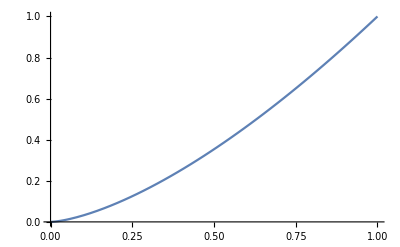

```mathematica
Plot[Δ^(3/2),{Δ,0,1}]
```

#### 1-order z*

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-Subscript[γ, 0,zz0]*t]*(1-Subscript[γ, 0,zz1]*t),{t,0,Infinity}]
```

ConditionalExpression[((γ_(0,zz0)-γ_(0,zz1)) v_z^2[0])/(γ_(0,zz0)^2),Re[γ_(0,zz0)]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.9,1}]
```

ConditionalExpression[1/ξ(0.0926266-0.197551 κ ξ+1.4803×10^-16 κ ξ Log[ξ]) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.8,1}]
```

ConditionalExpression[(-0.418394 κ+0.171027/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.7,1}]
```

ConditionalExpression[(-0.668766 κ+0.236015/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.6,1}]
```

ConditionalExpression[(-0.957798 κ+0.288458/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.5,1}]
```

ConditionalExpression[(-1.29965 κ+0.329289/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.4,1}]
```

ConditionalExpression[(-1.71805 κ+0.359523/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.3,1}]
```

ConditionalExpression[(-2.25745 κ+0.380282/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.2,1}]
```

ConditionalExpression[(-3.0177 κ+0.392845/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.1,1}]
```

ConditionalExpression[(-4.31735 κ+0.398735/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.01,1}]
```

ConditionalExpression[(-8.63469 κ+0.399996/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.005,1}]
```

ConditionalExpression[(-9.93435 κ+0.399999/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.004,1}]
```

ConditionalExpression[(-10.3527 κ+0.4/ξ) v_z^2[0],Re[ξ]>0]

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.003,1}]
```

Integrate::idiv: Integral of 1/24 (-(15 κ (-2.22045×10^-16+ⅇ^(-6085.81 t ξ) (-2.-12171.6 t ξ)+2 ⅇ^(-t ξ) (1+t ξ)))/t+(16 (Gamma[-2/3,t ξ]-Gamma[-2/3,6085.81 t ξ]))/(1/(t ξ))^(2/3)) v_z^2[0] does not converge on {0,∞}.

∫_0^∞ 1/24 (-(15 κ (-2.22045×10^-16+ⅇ^(-6085.81 t ξ) (-2.-12171.6 t ξ)+2 ⅇ^(-t ξ) (1+t ξ)))/t+(16 (Gamma[-2/3,t ξ]-Gamma[-2/3,6085.81 t ξ]))/(1/(t ξ))^(2/3)) v_z^2[0]ⅆt

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.001,1}]
```

Integrate::idiv: Integral of 1/24 (-(15 κ (-2.22045×10^-16+ⅇ^(-31622.8 t ξ) (-2.-63245.6 t ξ)+2 ⅇ^(-t ξ) (1+t ξ)))/t+(16 (Gamma[-2/3,t ξ]-Gamma[-2/3,31622.8 t ξ]))/(1/(t ξ))^(2/3)) v_z^2[0] does not converge on {0,∞}.

∫_0^∞ 1/24 (-(15 κ (-2.22045×10^-16+ⅇ^(-31622.8 t ξ) (-2.-63245.6 t ξ)+2 ⅇ^(-t ξ) (1+t ξ)))/t+(16 (Gamma[-2/3,t ξ]-Gamma[-2/3,31622.8 t ξ]))/(1/(t ξ))^(2/3)) v_z^2[0]ⅆt

```mathematica
Integrate[(Subscript[v, z]^2)[0]*Exp[-ξ/Δ^(3/2)*t]*(1-(15*κ*ξ^2)/(8*Δ^4)*t),{t,0,Infinity},{Δ,0.0,1}]
```

Integrate::idiv: Integral of -(1.25 ⅇ^(-1. t ξ) κ v_z^2[0])/t-1.25 ⅇ^(-1. t ξ) κ ξ v_z^2[0]+0.666667 ExpIntegralE[1.66667,t ξ] v_z^2[0] does not converge on {0,∞}.

∫_0^∞ ((ⅇ^(-1. t ξ) κ (-1.25-1.25 t ξ))/t+0.666667 ExpIntegralE[1.66667,t ξ]) v_z^2[0]ⅆt